```mathematica
(* Задача 1 *)
Div[{f1[y,z],g1[x,z],h1[x,y]},{x,y,z}]
(* Изведено и в листа*)
```

0

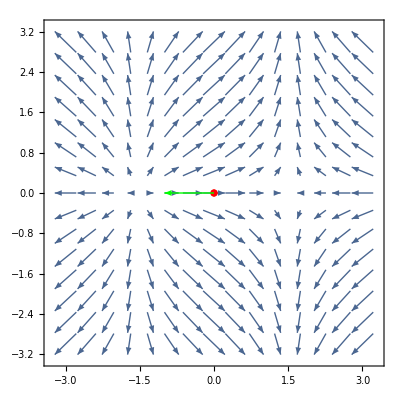

```mathematica
(* Задача 2 *)
Show[{VectorPlot[Grad[Sin[x]+Sqrt[y*y + 1],{x,y}]/.{x->s,y->t},{s,-3,3},{t,-3,3}],ListPlot[{{0,0}},PlotStyle->Red],
Graphics[{Green,Arrow[{{0,0},{0,0}-Grad[Sin[x]+Sqrt[y*y + 1],{x,y}]/.{x->0,y->0}}]}]}]
(* Посоката на потока ще е обратна на gradf, накъдето расте концентрацията, а дифузионният поток е от по-висока към по-ниска концентрация => по отрицателната посока на x. *)(* В зелено е потокът в (0,0) при допускането че дифузионната константа е 1 *)
```

-y/((1+y^2)^(3/2))

0

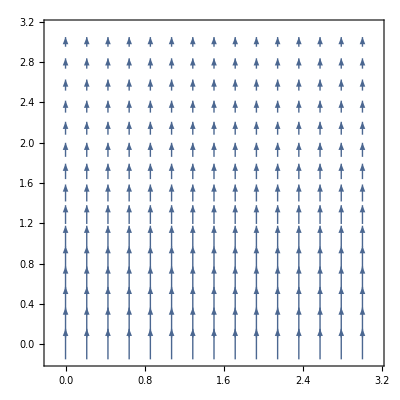

```mathematica
(* Задача 3 *)
(* divF < 0 от "по-големи стрелки" влизат в точките. Полето явно е безвихрово, откъдето и 2DcurlF=0 *)
(* Наподобява долното поле в първият квадрант *)
F[x_,y_]:={0,1/Sqrt[y*y +1]} (* И при нас всички вектори са насочени нагоре и втората им координата не зависи от x *)
Div[F[x,y],{x,y}]
Curl[F[x,y],{x,y}]
VectorPlot[F[x,y],{x,0,3},{y,0,3}]
(* Извел съм и в листа *)
```

```mathematica
(* Задача 4 *)
(* Намялява с растене на x => f_x < 0 *)
(* Расте с растене на y => f_y > 0 *)
(* Линиите на ниво започват да стават по-редки по посока x, и f започва да намалява по-бавно => f_xx > 0 *)
```

```mathematica
(* Задача 5 *)
f[x_]:=Sin[x[[1]]^2+x[[2]]^2+12]
f[{1,1}]==Sin[14] (* Наистина точката е от графиката на f *)
(* Може първо да пресметне градиентът и да се замести, а може и директно със субституция *)
(* Grad[f[{x,y}],{x,y}] *)
(*Plane[f_,x_,x0_]:=f[x0]+{2x0[[1]]Cos[x0[[1]]^2+x0[[2]]^2+12], 2x0[[2]]Cos[x0[[1]]^2+x0[[2]]^2+12]}.(x-x0)*)
Plane[f_,x_,x0_]:=f[x0]+(Grad[f[{u,v}],{u,v}]/.{u->x0[[1]],v->x0[[2]]}).(x-x0)
Plot3D[{f[{x,y}],Plane[f,{x,y},{1,1}]},{x,0,2},{y,0,2}]
```

True

-Graphics3D-

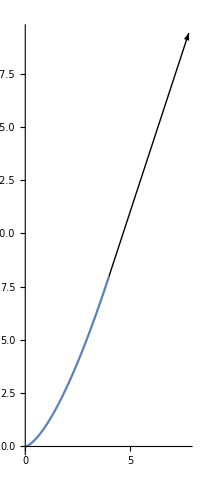

```mathematica
(* Задача 6 *)
tEnd=2;
r[t_]:={t^2,t^3}
(* Векторът на скоростта е *)
v[t_] := D[r[s],s]/.{s->t}
(* Единичният тангенциален вектор T се задава чрез *)
tang[t_]:=Normalize[v[t]]
(* Ускорението е *)
a[t_]:=D[v[s],s]/.{s->t}
(* Тангенциалното ускорението е вектор-проекцията на a върху посока T *)
aComponent[t_]:=a[t].tang[t] (* Тангенциалната компонента на ускорението *)
aTang[t_]:=aComponent[t] tang[t] (* Използваме, че Т е единичен *)
Show[
{ParametricPlot[r[t],{t,0,tEnd}, PlotRange->All],
Graphics[Arrow[{r[tEnd],r[tEnd]+aTang[tEnd]}]]
}]
```

```mathematica
(* Задача 7 *)
tEnd=2Pi;
r[t_]:={Sin[t],Cos[t]}
(* Векторът на скоростта е *)
v[t_] := D[r[s],s]/.{s->t}
(* Единичният тангенциален вектор T се задава чрез *)
tang[t_]:=Normalize[v[t]]
(* Кривината е *)
κ[t_]:=Norm[D[tang[s],s]/.{s->t}]/Norm[v[t]]
(* Нормалният вектор N е ортогонален на тангенциалният T. В зависимост от това коя нормала желаем, взимаме едно от двете n[t_] по-долу *)
n[t_]:=D[tang[s],s]/.{s->t}
(*n[t_]:=-D[tang[s],s]/.{s->t}*)
(* Векторното поле *)
F[x_,y_]:= {Sqrt[x^2+1],Sqrt[x^2+y^2]}
(* Търсената нормална компонента. Защо точно Pi/4 съм написал в листа *)
F[(√2)/2,(√2)/2].n[Pi/4]
(* κ[t], Mathematica дава сложен израз, т.к. слага ненужни абсолютни стойности *)
```

-1/(√2)-(√3)/2

```mathematica
(* Задача 8 е изцяло на листа *)
(* Дори не съм сигурен дали може да се покаже на Mathematica *)
```

```mathematica
(* Задача 9 *)
x[ρ_,ϕ_,θ_]:=ρ Sin[ϕ]Cos[θ]
y[ρ_,ϕ_,θ_]:=ρ Sin[ϕ]Sin[θ]
z[ρ_,ϕ_,θ_]:=ρ Cos[ϕ]
givenGrad = {1,2,-2};
(* Защо имаме право съм показал на лист *)
givenGrad.(D[{x[ρ,ϕ,θ],y[ρ,ϕ,θ],z[ρ,ϕ,θ]},ϕ]/.{ρ->2,ϕ->Pi/4,θ->-Pi/4})
```

-1+2 √2

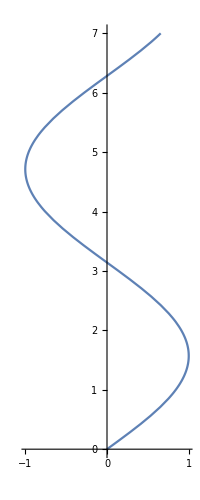

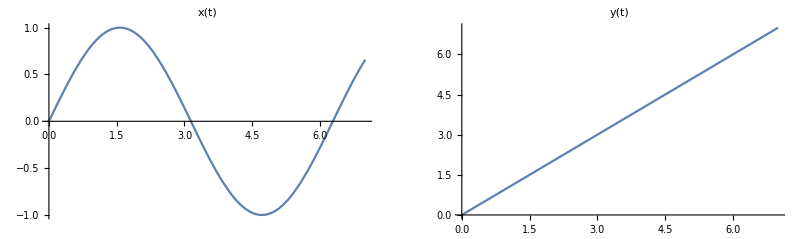

```mathematica
(* Задача 10 *)
(* Скицирано и на листа, но изглежда като да е следната крива *)
r[t_]:={Sin[t],t}
ParametricPlot[r[t],{t,0,7}]
(* Оттук x=sin t y=t *)
GraphicsGrid[{{Plot[Sin[t],{t,0,7},PlotLabel->"x(t)"],Plot[t,{t,0,7},PlotLabel->"y(t)"]}}]
```